## §4. Применение степенных рядов

### 4.1. Интегрирование функций.

Разлагая подынтегральную функцию f(t) в степенной ряд, можно, используя теорему об интегрировании степенных рядов, представить интеграл ∫_0^x f(t)ⅆt в виде степенного ряда и подсчитать величину этого интеграла с заданной точностью при любом значении x из интервала сходимости полученного ряда.

##### Пример №12.289

Разложить указанную функцию в степенной ряд по степеням x:

f(x)=∫_0^x (ln(1+t^2))/t ⅆt

Используем разложение функции ln(1+y):

```mathematica
series[y,0,Log[1+y]]
```

((-1)^(n+1) y^n)/nn0∞

Заменив y→ t^2 и разделив на t, получим ряд:

∑_(n=0)^∞ (-1)^(n+1)t^(2n-1)/n

По теореме о интегрировании степенных рядов получаем:

∫_0^x ∑_(n=0)^∞ (-1)^(n+1)t^(2n-1)/n ⅆt=∑_(n=0)^∞ (-1)^(n+1)/n∫_0^x t^(2n-1)ⅆt=∑_(n=0)^∞ (-1)^(n+1)x^(2n)/(2 n^2)

Ту же последовательность действий можно проделать, используя средства Wolfram Mathematica:

Сразу находим разложение подынтегральной функции:

```mathematica
Series[Log[1+t^2]/t,{t,0,8}]
```

t-t^3/2+t^5/3-t^7/4+O[t]^9

Интегрируем по t от 0 до x и получаем искомый ряд:

```mathematica
Integrate[Series[Log[1+t^2]/t,{t,0,10}],t]/.t-> x
```

x^2/2-x^4/8+x^6/18-x^8/32+x^10/50+O[x]^12

Найти n-ый коэффициент можно следующим образом:

```mathematica
Simplify[SeriesCoefficient[Log[1+t^2]/t,{t,0,n}],n>0]*1/(n+1)
```

(ⅈ ((-ⅈ)^n-ⅈ^n))/(1+n)^2

Множитель 1/(n+1) появился из-за интегрирования функции t^n.

Ответ:

∫_0^x (ln(1+t^2))/t ⅆt=∑_(n=0)^∞ (-1)^(n+1)x^(2n)/(2 n^2)

##### Пример №12.300

Вычислить интеграл с точностью до 10^-5:

∫_0^1 (sin(t))/t ⅆt

Получим разложение заданной функции в ряд :

```mathematica
ser=Integrate[Series[Sin[t]/t,{t,0,10}],t]/.t-> x
```

x-x^3/18+x^5/600-x^7/35280+x^9/3265920-x^11/439084800+O[x]^12

Теперь, заменяя x на нужное нам значение x=1, получаем:

```mathematica
N[Normal@ser/.x-> 1]
```

0.946083

Функция Normal необходима, чтобы отбросить остаток ряда O[x]^12

Получили искомое значение интеграла.

### 4.2. Интегрирование дифференциальных уравнений с помощью рядов.

Степенные ряды широко применяются при решении дифференциальных уравнений. Для целого ряда дифференциальных уравнений показано, что решение y(t) представимо в виде степенного ряда

y(x)=∑_(k=0)^∞ (a_k(x-x_0))^k=∑_(k=0)^∞ (y^(k)(x_0))/(k!)(x-x_0)^k

коэффициенты которого можно определить с учетом заданного уравнения различными способами.

а) Пусть требуется найти решение уравнения y''=f(x,y,y'), удовлетворяющее условиям y(x_0)=y_0, y'(x_0)=y_1, причем функция f(x,y,y') в точке (x_0,y_0,y_1) имеет частные производные любого порядка. Тогда коэффициенты y^(k)(x_0) ряда (1) определяются путем последовательного дифференцирования исходного уравнения и подстановки в него x_0 и найденных уже значений y'(x_0), y''(x_0)...

##### Пример №12.326

Найти решение уравнения, удовлетворяющее заданным условиям:

y''=-x^2y'-2x y+1, y(0)=y'(0)=0

Для того чтобы записать решение в форме (1), продифференцируем данное уравнение несколько раз:

```mathematica
Table[D[y''[x]==-x^2 y'[x]-2x y[x]+1,{x,n}],{n,1,6}]//TableForm
```

y^(3)[x]==-2 y[x]-4 x y'[x]-x^2 y''[x]
y^(4)[x]==-6 y'[x]-6 x y''[x]-x^2 y^(3)[x]
y^(5)[x]==-12 y''[x]-8 x y^(3)[x]-x^2 y^(4)[x]
y^(6)[x]==-20 y^(3)[x]-10 x y^(4)[x]-x^2 y^(5)[x]
y^(7)[x]==-30 y^(4)[x]-12 x y^(5)[x]-x^2 y^(6)[x]
y^(8)[x]==-42 y^(5)[x]-14 x y^(6)[x]-x^2 y^(7)[x]

Теперь можно заметить следующую закономерность, которую мы запишем в виде:

y^(n+2)(x)=-n(n+1)y^(n-1)(x)-2(n+1)x y^(n)(x)-x^2 y^(n+1)(x), при n>2

Подставляя x_0=0 получим, следующее выражение:

y^(n+2)(0)=-n(n-1)y^(n-1)(0)

Или по-другому:

y^(n)(0)=-(n-1)(n-2)y^(n-3)(0)

Мы получили рекуррентное уравнение. Определим начальные условия, два из которых  нам уже даны, а еще одно получается при подстановке x_0=0 в исходное уравнение:

y(0)=y'(0)=0,y''(0)=1

Составим формулу для значения n-ой производной функции y с помощью опции Piecewise:

```mathematica
yn[n_]:=Piecewise[{{-(n-1)(n-2)yn[n-3],n≥3},{1,n==2},{0,n<2}}]
```

Протабулируем функцию от 0 до 12:

```mathematica
Table[yn[n],{n,0,18}]
```

{0,0,1,0,0,-12,0,0,504,0,0,-45360,0,0,7076160,0,0,-1698278400,0}

Мы получили ничто иное как коэффициенты разложения искомой функции в ряд.

Теперь запишем сам ряд по формуле (1):

```mathematica
Sum[yn[k]/(k!)x^k,{k,0,18}]
```

x^2/2-x^5/10+x^8/80-x^11/880+x^14/12320-x^17/209440

Введем функцию y1(x,n):

```mathematica
y1[x_,n_]:=Sum[yn[k]/(k!)x^k,{k,0,n}]
```

y1(x,n) - искомая функция, являющаяся решением исходного дифференциального уравнения.

Решим задачу другим способом.

После того как мы получили рекуррентное уравнение:

y^(n)(0)=-(n-1)(n-2)y^(n-3)(0)

решим его с помощью встроенной функции для решения рекуррентных уравнений RSolve[ expr, f[n], n]:

```mathematica
sol=RSolve[{y[n]==-(n-1)(n-2)y[n-3],y[0]==y[1]==0,y[2]==1},y[n],n]
```

{{y[n]→((-1)^(1/3) 3^(-5/6-n/3) Gamma[5/3] Gamma[1+n] ((-1)^(1+n/3) √3+(-1)^(n/3) √3 Cos[(2 n π)/3]+3 (-1)^(n/3) Sin[(2 n π)/3]))/(2 Gamma[1+n/3])}}

Мы получили громоздкую функцию, однако, если построить список ее значений от 0 до 18, то можно убедиться, что значения коэффициентов совпадают с уже ранее полученными в функции yn(n):

```mathematica
Table[y[n]/.Flatten@sol,{n,0,18}]//N
```

{0.,0.,1.,0.,0.,-12.,0.,0.,504.,0.,0.,-45360.,0.,0.,7.07616×10^6,0.,0.,-1.69828×10^9,0.}

Значения коэффициентов не изменились, значит задавать новую функцию не имеет смысла.

Решим задачу с помощью встроенной в систему функции для решения дифференциальных уравнений DSolve[expr, y[x], x]:

```mathematica
sol1=DSolve[{y''[x]==-x^2 y'[x]-2x y[x]+1,y[0]==y'[0]==0},y[x],x]
```

{{y[x]→-(ⅇ^(-x^3/3) ((-1)^(1/3) x Gamma[2/3]-(-x^3)^(1/3) Gamma[2/3,-x^3/3]))/(3^(1/3) x)}}

Введем функцию y3(x):

```mathematica
y3[x_]:=y[x]/.sol1
```

Докажем графически, что полученная в данном случае функция совпадает с функцией y1(x,18):

```mathematica
Plot[{y3[x],y1[x,18]},{x,0,2}]
```

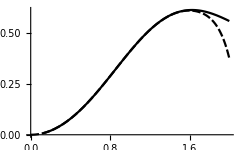

Как мы видим, расхождение начинается примерно с x=1.5, что, разумеется, объясняется малым порядком (n=18) разложения.

Наконец, докажем, что полученное решение верно, непосредственно подставив функцию y3(x) в исходное дифференциальное уравнение:

```mathematica
D[y3[x],{x,2}]==-x^2 D[y3[x],x]-2x y3[x]+1//FullSimplify
```

```mathematica
True
```

Задача решена.

б) Если исходное дифференциальное уравнение линейно относительно искомой функции и ее производных, причем коэффициент при старшей производной в точке x_0 отличен от нуля, то решение следует искать в виде ряда (1) с неопределенными коэффициентами a_k,k=0,1... Законность такого метода вытекает из утверждения, доказываемого в аналитической теории дифференциальных уравнений, которое мы приведем для уравнения 2-ого порядка.

Т е о р е м а 1. Если в дифференциальном уравнении

p_0(x)y''+p_1(x)y'+p_2(x)y=f(x)

функции p(x), p_1(x),p_2(x) и f(x) аналитичны в окрестности точки x_0, и p_0(x_0)≠ 0, то существует решение уравнения (2), представимое в виде степенного ряда (3):

y(x)=∑_(k=0)^∞ (a_k(x-x_0))^k

##### Пример №12.330

Используя степенные ряды, проинтегрировать следующее дифференциальное уравнение:

y''+x y'+y=1, y(0)=y'(0)=0

Введем функцию y(x) по формуле (3):

```mathematica
y[x_]:=Sum[Subscript[a, k] x^k,{k,0,Infinity}]
```

Подставим ее в исходное дифференциальное уравнение:

```mathematica
D[y[x],{x,2}]+x D[y[x],x]+y[x]==1//FullSimplify//TraditionalForm
```

∑_(k=0)^∞ (k-1) k a_k x^(k-2)+x ∑_(k=0)^∞ k a_k x^(k-1)+∑_(k=0)^∞ a_k x^k==1

Учтём начальные условия: при k=0,1 a_k=0, а при k=2 и x=0:

1·2 a_2+0+0=1⇒a_2=1/(2·1)

Теперь составим следующее рекуррентное соотношение:

((k+2)-1)(k+2)a_(k+2)+k a_k+a_k=0
(k+1)(k+2)a_(k+2)=-(k+1)a_k
a_(k+2)=-a_k/(k+2)

Запишем функцию для коэффициента a_k, заданного следующим образом:

a_k=Piecewise[{{-(a_(k-2))/k, k≥ 3}, {1/2, k==2}, {0, k<2}}]

```mathematica
ak[k_]:=Piecewise[{{(-ak[k-2])/k,k≥ 3},{0,k<2},{1/2,k==2}}]
```

Протабулируем функцию на отрезке от 0 до 12:

```mathematica
Table[ak[k],{k,0,12}]
```

{0,0,1/2,0,-1/8,0,1/48,0,-1/384,0,1/3840,0,-1/46080}

Теперь можно записать ряд (3):

```mathematica
Sum[ak[k] x^k,{k,0,12}]
```

x^2/2-x^4/8+x^6/48-x^8/384+x^10/3840-x^12/46080

Данный ряд является решением исходного дифференциального уравнения при заданных начальных условиях. Зададим функцию y1(x,n):

```mathematica
y1[x_,n_]:=Sum[ak[k] x^k,{k,0,n}]
```

Теперь решим ту же задачу, используя функцию DSolve:

```mathematica
sol=DSolve[{D[y[x],{x,2}]+x D[y[x],x]+y[x]==1,y[0]==0,y'[0]==0},y[x],x]
```

{{y[x]→ⅇ^(-x^2/2) (-1+ⅇ^(x^2/2))}}

```mathematica
y2[x_]:=ⅇ^(-x^2/2) (-1+ⅇ^(x^2/2))
```

Построим график функций y1(x,24) и функции полученной с помощью DSolve:

```mathematica
Plot[{y2[x],y1[x,24]},{x,-4,4}]
```

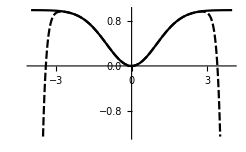

Так как функции совпадают приблизительно до |x|=2.5, будем считать, что решение в окрестности точки x_0=0 получено верно.

Еще в этом можно убедится, подставив функцию в общем виде в исходное дифференциальное уравнение:

```mathematica
D[y2[x],{x,2}]+x D[y2[x],x]+y2[x]==1//FullSimplify
```

True

Получили верное равенство.

Замечание: в том что ряд был получен верно, можно также убедиться, разложив функцию y2(x)  в ряд по степеням x:

```mathematica
Series[y2[x],{x,0,12}]
```

x^2/2-x^4/8+x^6/48-x^8/384+x^10/3840-x^12/46080+O[x]^13

Ряды совпадают, значит на данном этапе будем считать, что решение получено верно.

### 4.3. Уравнение и функции Бесселя.

Частным случаем уравнения (2) является уравнение Бесселя

x^2 y''+x y'+(x^2-v^2)y=0

Его решениями являются цилиндрические функции Бесселя первого рода порядка v

J_v(x)=a_0^(v)x^v∑_(k=0)^∞ (-1)^k/(k!(v+1)(v+2)...(v+k))(x/2)^(2k)

и для нецелых v

J_-v(x)=a_0^(v)x^-v∑_(k=0)^∞ (-1)^k/(k!(1-v)(2-v)...(k-v))(x/2)^(2k)

Если же v - целое число, v=n, то вторым частным решением уравнения Бесселя (4) является функция Неймана (или Вебера), определяемая из соотношения

N_n(x)=lim_(v→n) (I_v(x)cos v π-I_-v(x))/(sin v π)

являющаяся цилиндрической функцией второго рода порядка n.

Формулы (5) и (6) можно упростить с помощью гамма-функции, которая определена равенством

Г(v)=∫_0^(+∞) ⅇ^-x x^(v-1)ⅆx

Этот несобственный интеграл сходится для всех v>0. Гамма-функция - обобщение для x>0 функции факториала n!, которая определена только если n - натуральное число. Рассмотрим предел:

(Г(1)=∫_0^(+∞) ⅇ^-x ⅆx=lim_(b→+∞) -ⅇ^-x|)_0^b=1

Теперь найдем интеграл:

(Г(v+1)=∫_0^(+∞) ⅇ^-x x^v ⅆx=Г(1)=lim_(b→+∞) -ⅇ^-x x^v|)_0^b+∫_0^(+∞) v ⅇ^-x x^(v-1)ⅆx=
=v ∫_0^(+∞) ⅇ^-x x^(v-1)ⅆx

Таким образом мы получаем равенство:

Г(v+1)=v Г(v)

Это важнейшее свойство гамма-функции.

Г(2)=1· Г(1)=1!, Г(3)=2·Г(2)=2!,..., Г(n+1)=n!

Теперь, если положить a_0^(v)  в формулах (5) и (6)

a_0^(v)=1/(2^v Г(v+1))

и заметить, что

Г(v+k+1)=(v+k)(v+k-1)...(v+2)(v+1)Г(v+1)

то тогда можно записать функцию Бесселя первого рода кратко с помощью гамма-функции:

J_v(x)=∑_(k==0)^∞ (-1)^k/(k!Г(v+k+1))(x/2)^(2k+v)

J_-v(x)=∑_(k=0)^∞ (-1)^k/(k!Г(-v+k+1))(x/2)^(2k-v)

Параметрическое уравнение Бесселя порядка v имеет вид:

x^2 y''+x y'+(α^2 x^2-v^2)y=0, α>0

Заменой t=α x преобразовываем это уравнение в стандартное уравнение Бесселя:

t^2 y''+t y'+(t^2-v^2)y=0

Имеющее общее решение:

y(x)=c_1 J_v(α x)+c_2 J_-v(α x)- если v - не целое число,
y(x)=c_1 J_v(α x)+c_2 N_v(α x)- если v -  целое число.

##### Пример №12.342

Найти общее решение уравнения

x^2 y'' +x y'+ (9 x^2-1/25)y=0

Функция Бесселя в Mathematica записывается BesselJ[v,x]. Построим два графика: J_(1/5)(3x) и J_(-1/5)(3x):

```mathematica
Plot[{BesselJ[1/5,x],BesselJ[-1/5,x]},{x,0,15},PlotLabels->{"J_(1/5)(3x)","J_(-1/5)(3x)"}]
```

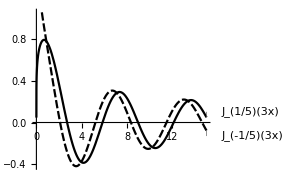

Ответом, общим решением этого параметрического уравнения, является функция y(x), определяемая:

y(x)=c_1 J_(1/5)(3x)+c_2 J_(-1/5)(3x)